```mathematica
OS="win";(*or,linux*)
Needs["ErrorBarPlots`"];
Needs["EDA`"];
Needs["CustomTicks`"];
SetOptions[LinTicks,TickLabelStep->1,MajorTickLength->{0.0125,0},MinorTickLength->{0.0075,0}];
If[OS=="win",
Print["Working Directory: ",descDir="C:\\Users\\tmpra\\Dropbox\\nEDM\\daq-tools-bkg-auto\\nstar_online"];Print["(AscDir) Rawdata Directory: ",AscDir="C:\\Users\\tmpra\\Dropbox\\nEDM\\rawdata"];Print["(ScrDir) Scratch Directory: ",curDir=SetDirectory["C:\\Users\\tmpra\\Dropbox\\Scratch"]];Print["(PicDir) Picture Directory: ",PicDir="C:\\Users\\tmpra\\Dropbox\\nEDM\\Pictures"];Print["(SysDir) System Directory: ",SysDir="C:\\Users\\tmpra\\Dropbox\\nEDM\\system"];
Print["Rawdata on mpc1636:",mpcDir="/xdata/nedm_data/RawData"];
seperator="\\";
];
If[OS=="axion",
Print["Working Directory: ",descDir="/home/prajwal/Dropbox/nEDM/daq-tools-bkg-auto/nstar_online"];Print["(AscDir) Rawdata Directory: ",AscDir="/home/prajwal/Dropbox/nEDM/rawdata"];Print["(ScrDir) Scratch Directory: ",curDir=SetDirectory["/home/prajwal/Dropbox/Scratch"]];Print["(PicDir) Picture Directory: ",PicDir="/home/prajwal/Dropbox/nEDM/Pictures/nstar/runs"];Print["(SysDir) System Directory: ",SysDir="/home/prajwal/Dropbox/nEDM/system"];
Print["Rawdata on mpc1636:",mpcDir="/xdata/nedm_data/RawData"];
seperator="/";
];
metaStructure={Word,Real,Real,Word,Real,Real,Word,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Word,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Word,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Word,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real};
metadesc={Number,Number,Number,Number,Number,Number,Number,Word,Real,Real,Real,Real};
descdat=ReadList[StringJoin[descDir,seperator,"desctf_c.dat"],metadesc];
dimdesc=Dimensions[descdat][[1]];
metalvl3={Real,Real,Real,Real,Real,Real,Real,Real};
tk2[l_,u_,a_,b_,c_,d_,int_]:=SetPrecision[N[Table[{10^j,Superscript["10",j],{a,b}},{j,l,u,int}]~Join~Table[{10^j,"",{c,d}},{j,l+int/2,u-int/2,int}]],3];
tk3[l_,u_,a_,b_,c_,d_,int_]:=Table[{j,Ceiling[j],{a,b}},{j,l,u,int}]~Join~Table[{j,"",{c,d}},{j,l+int/2,u-int/2,int}];
```

Working Directory: C:\Users\tmpra\Dropbox\nEDM\daq-tools-bkg-auto\nstar_online

(AscDir) Rawdata Directory: C:\Users\tmpra\Dropbox\nEDM\rawdata

(ScrDir) Scratch Directory: C:\Users\tmpra\Dropbox\Scratch

(PicDir) Picture Directory: C:\Users\tmpra\Dropbox\nEDM\Pictures

(SysDir) System Directory: C:\Users\tmpra\Dropbox\nEDM\system

Rawdata on mpc1636:/xdata/nedm_data/RawData

# Papers: e.cm

## [1] On the Possibility of Electric Dipole Moments for Elementary Particles and Nuclei, E.M. Purcell, N.F. Ramsey, Phys.Rev. 78 (1950) 807-807. DOI: 10.1103/PhysRev.78.807. --- [2] Experimental limit to the electric dipole moment of the neutron, J.H. Smith, E.M. Purcell, N.F. Ramsey, Phys.Rev. 108 (1957) 120-122. DOI: 10.1103/PhysRev.108.120 [3] Limit to the Electric Dipole Moment of the Neutron, P.D. Miller, W.B. Dress, J.K. Baird, Norman F. Ramsey, Phys.Rev.Lett. 19 (1967) no.7, 381. DOI: 10.1103/PhysRevLett.19.381 [4] Upper Limit for the Electric Dipole Moment of the Neutron, W.B. Dress, J.K. Baird, P.D. Miller, Norman F. Ramsey, Phys.Rev. 170 (1968) no.5. DOI: 10.1103/PhysRev.170.1200 [6] Improved upper limit to the electric dipole moment of the neutron J.K. Baird, P.D. Miller, W.B. Dress, N.F. Ramsey, Phys.Rev. 179 (1969) 1285-1291. DOI: 10.1103/PhysRev.179.1285 [7] Improved upper limit for the electric dipole moment of the neutron, W.B. Dress, P.D. Miller, N.F. Ramsey, Phys.Rev. D7 (1973) 3147-3149. DOI: 10.1103/PhysRevD.7.3147 [8] Search for an Electric Dipole Moment of the Neutron, W.B. Dress, P.D. Miller, J.M. Pendlebury, Paul Perrin, Norman F. Ramsey, Phys.Rev. D15 (1977) 9. DOI: 10.1103/PhysRevD.15.9 --- [5] Search for a Neutron Electric Dipole Moment by a Scattering Experiment, C.G. Shull, R. Nathans, Phys.Rev.Lett. 19 (1967) 384-386. DOI: 10.1103/PhysRevLett.19.384 --- [6b] Electric dipole moment of the neutron, V.W. Cohen, R. Nathans, H.B. Silsbee, E. Lipworth, N.F. Ramsey, Phys.Rev. 177 (1969) 1942-1945. DOI: 10.1103/PhysRev.177.1942 --- [9] A search for the electric dipole moment of the neutron using ultracold neutrons, I.S. Altarev, Yu.V. Borisov, A.B. Brandin, A.I. Egorov, V.F. Ezhov, S.N. Ivanov, V.M. Lobashov, V.A. Nazarenko, G.D. Porsev, V.L. Ryabov et al., Nucl.Phys. A341 (1980) 269-283. DOI: 10.1016/0375-9474(80)90313-9 [10] A New Upper Limit on the Electric Dipole Moment of the Neutron, I.S. Altarev, Yu.V. Borisov, N.V. Borovikova, A.B. Brandin, A.I. Egorov, V.F. Ezhov, S.N. Ivanov, V.M. Lobashev, V.A. Nazarenko, V.L. Ryabov et al., Phys.Lett. 102B (1981) 13-16. DOI: 10.1016/0370-2693(81)90202-1 [10b] IS Altarev, YV Borisov, NV Borovikova, AB Brandin, AI Egorov, SN Ivanov, É. A. Kolomenskii, MS Lasakov, VM Lobashev, AN Pirozhkov, AP Serebrov, Y. V. Sobolev, R. R. Tal’Daev, and B. V. Shul’Gina. Search for an electric dipole moment of the neutron. Soviet Journal of Experimental and Theoretical Physics Letters, 44:460, October 1986. DOI: 10.1016/B978-0-444-88081-9.50040-0 [11] New measurement of the electric dipole moment of the neutron, I.S. Altarev, Yu.V. Borisov, N.V. Borovikova, S.N. Ivanov, E.A. Kolomensky, M.S. Lasakov, V.M. Lobashev, V.A. Nazarenko, A.N. Pirozhkov, A.P. Serebrov et al., Phys.Lett. B276 (1992) 242-246. DOI: 10.1016/0370-2693(92)90571-K [11b] IS Altarev, YV Borisov, NV Borovikova, AI Egorov, SN Ivanov, EA Kolomensky, MS Lasakov, VM Lobashev, VA Nazarenko, AN Pirozhkov, A. P. Serebrov, Y. V. Sobolev, and E. V. Shulgina. Search for the neutron electric dipole moment. Physics of Atomic Nuclei, 59:1152–1170, July 1996. DOI: 10.1134/1.854647 [11c] New measurements of the neutron electric dipole moment, A.P. Serebrov, E.A. Kolomenskiy, A.N. Pirozhkov, I.A. Krasnoshсhekova, A.V. Vasil’ev, A.O. Polushkin, M.S. Lasakov, A.K. Fomin, I.V. Shoka, V.A. Solovei et al., JETP Lett. 99 (2014) 4-8. DOI: 10.1134/S0021364014010111. arXiv:1310.5588 [11d] New search for the neutron electric dipole moment with ultracold neutrons at ILL, A.P. Serebrov, E.A. Kolomenskiy, A.N. Pirozhkov, I.A. Krasnoschekova, A.V. Vassiljev, A.O. Ilyushin, M.S. Lasakov, A.N. Murashkin, V.A. Solovey, A.K. Fomin et al., Phys.Rev. C92 (2015) no.5, 055501. DOI: 10.1103/PhysRevC.92.055501 --- [12] Search for a Neutron Electric Dipole Moment, J.M. Pendlebury, K.F. Smith, R. Golub, J. Byrne, Phys.Lett. 136B (1984) 327-330. DOI: 10.1016/0370-2693(84)92013-6 [13] A Search for the Electric Dipole Moment of the Neutron, K.F. Smith, N. Crampin, J.M. Pendlebury, D.J. Richardson, D. Shiers, K. Green, A.I. Kilvington, J. Moir, H.B. Prosper, D. Thompson et al., Phys.Lett. B234 (1990) 191-196. DOI: 10.1016/0370-2693(90)92027-G [14] New experimental limit on the electric dipole moment of the neutron, P.G. Harris, C.A. Baker, K. Green, P. Iaydjiev, S. Ivanov (Rutherford), D.J.R. May, J.M. Pendlebury, D. Shiers, K.F. Smith, M. van der Grinten et al., Phys.Rev.Lett. 82 (1999) 904-907. DOI: 10.1103/PhysRevLett.82.904 [15] An Improved experimental limit on the electric dipole moment of the neutron, C.A. Baker, D.D. Doyle, P. Geltenbort, K. Green, M.G.D. van der Grinten, P.G. Harris, P. Iaydjiev, S.N. Ivanov, D.J.R. May, J.M. Pendlebury et al., Phys.Rev.Lett. 97 (2006) 131801. DOI: 10.1103/PhysRevLett.97.131801. arXiv: hep-ex/0602020 --- [16] Revised experimental upper limit on the electric dipole moment of the neutron, J. M. Pendlebury, S. Afach, N.J. Ayres, C.A. Baker, G. Ban, G. Bison, K. Bodek, M. Burghoff, P. Geltenbort, K. Green et al., Phys.Rev. D92 (2015) no.9, 092003. DOI: 10.1103/PhysRevD.92.092003 --- [17] Measurement of the neutron electric dipole moment via spin rotation in a non-centrosymmetric crystal, V.V. Fedorov, M. Jentschel, I.A. Kuznetsov, E.G. Lapin, E. Lelievre-Berna, V. Nesvizhevsky, A. Petoukhov, S.Yu. Semenikhin, T. Soldner, V.V. Voronin et al., Phys.Lett. B694 (2011) 22-25. DOI: 10.1016/j.physletb.2010.09.033. arXiv:1009.0153 --- [18] Reduced Limit on the Permanent Electric Dipole Moment of Hg199, B. Graner, Y. Chen, E.G. Lindahl, B.R. Heckel, Phys.Rev.Lett. 116 (2016) no.16, 161601. Erratum: Phys.Rev.Lett. 119 (2017) no.11, 119901. DOI: 10.1103/PhysRevLett.119.119901, 10.1103/PhysRevLett.116.161601. arXiv:1601.04339

### [1] ANL [2][3][4][6][7][8]: ORNL [5][6b]: BNL [9][10][10b][11][11b][11c][11d]: LNPI, New PNPI: Double Chamber - ILL (then Gatchina) [12][13][14]: RAL-Sussex-ILL [15][16]: Sussex-ILL-PSI [17] Bragg

## [1] 06.1950; <3E-18 --- [2] 10.1957; (.1±2.4)E-20 [3] 08.1967; (2±3)E-22 [4] 06.1968; (-0.3±0.8)E-22, 3E-22 [6] 03.1969; (1.54±1.12)E-23, 5E-23 [7] 01.1973; (3.2±7.5)E-24, 1E-23 [8] 06.1977; (0.4±1.5)E-24, 3E-24 --- [5] 08.1967; (2.4±3.9)E-22 --- [6b] 01.1969; -, 1E-21 --- [9] 06.1980; (4±7.55)E-25, 1.6E-24 [10] 06.1981; (2.1±2.4)E-25, (2.3±2.3)E-25 (combining with before), 6E-25 [10b] 10.1986; (1.4±0.6)E-25 [11] 02.1992; (2.6±4.2±1.6)E-26, 1.1E-25 [11b] 07.1996; (2.6±4.0±1.6)E-26 [11c] 03.2014; (0.36±4.68)E-26 ?[11d, combines all old] 08.2015; (0.56 ± 3.04)E-26 -> 5.5E-26e.cm --- [12] 03.1984; (+0.3 ± 4.8)E-25 [13] 01.1990; −(3±5)E-26 [14] 02.1999; (1.0±3.6)E-26, 6.3E-26 [15] 09.2006; (0.2±1.5±0.7)E-26, 2.9E-26 --- [16] 11.2015; (0.21±1.82)E-26, 3E-26 --- PSI nEDM --- [17] 10.2010; (2.5 ± 6.5 ± 5.5)E-24 --- [18] 08.2017; (2.20±2.75±1.48)E-30 ×32176 (n:Hg EDM ratio)

```mathematica
Sqrt[2.75^2+1.48^2]*1.6485*32176
```

165649.

```mathematica
thk=.003;
Options[errListPlot]={Filling->{{2->{1}}},Joined->{False,False,True},PlotStyle->{Black,Black,Directive[Opacity[1],Blue]},FillingStyle->Black,PlotMarkers->{Graphics@Line[.04 {{-1,0},{1,0}}],Graphics@Line[.04 {{-1,0},{1,0}}],""}};
errListPlot[plotFun_,data_,opts:OptionsPattern[]]:=Block[{},plotFun[{{#[[1]],If[Sign[N[#[[2]]-#[[3]]]]<0,N[10^(-30)],Abs[#[[2]]-#[[3]]]]}&/@data,{#[[1]],#[[2]]+#[[3]]}&/@data,data[[;;,{1,2}]]},opts,Sequence@@Options[errListPlot]]];
marker[prim_,opts___][in_: White,out_: Black,size_: 22]:=Graphics[{in,EdgeForm[{AbsoluteThickness[2],Opacity[1],out}],prim},opts,ImageSize->size];
square=marker@Rectangle[];
circle=marker@Disk[];
diamond=marker@Polygon[{{0,1},{1,2},{2,1},{1,0}}];
triangle=marker[Polygon[{{1,0},{0,Sqrt[3]},{-1,0}}]];
triangle2=marker[Polygon[{{1,1+0},{0,1-Sqrt[3]},{-1,1+0}}]];
hglas=marker[Polygon[{{-1,-1+Sqrt[3]/2},{1,1+Sqrt[3]/2},{-1,1+Sqrt[3]/2},{1,-1+Sqrt[3]/2}}]];
starz=marker[Polygon[{{-1,0},{0,Sqrt[3]},{1,0},{-Sqrt[2],Sqrt[3]/2},{Sqrt[2],Sqrt[3]/2},{-1,0}}]];
pent=marker[Polygon[{{-1,0},{-Sqrt[2],Sqrt[3]/2},{0,Sqrt[3]},{Sqrt[2],Sqrt[3]/2},{1,0}}]];
acdat={
{
{N[1950+(6/12)],PlusMinus[.1,3]*10^(-18)}
},
{
{N[1957+(10/12)],PlusMinus[.1,2.4]*10^(-20)},
{N[1967+(8/12)],PlusMinus[2,3]*10^(-22)},
{N[1968+(8/12)],PlusMinus[.3,.8]*10^(-22)},
{N[1969+(3/12)],PlusMinus[1.54,1.12]*10^(-23)},
{N[1973+(1/12)],PlusMinus[3.2,7.5]*10^(-24)},
{N[1977+(6/12)],PlusMinus[0.4,1.5]*10^(-24)}
},
{
{N[1967+(8/12)],PlusMinus[2.4,3.9]*10^(-22)}
},
{
{N[1969+(1/12)],PlusMinus[0.1,1]*10^(-21)}
},
{
{N[1980+(6/12)],PlusMinus[4,7.55]*10^(-25)},
{N[1981+(6/12)],PlusMinus[2.1,2.4]*10^(-25)},
{N[1986+(10/12)],PlusMinus[1.4,0.6]*10^(-25)},
{N[1992+(2/12)],PlusMinus[2.6,Sqrt[4.2^2+1.6^2]]*10^(-26)},
{N[1996+(7/12)],PlusMinus[2.6,Sqrt[4.0^2+1.6^2]]*10^(-26)},
{N[2014+(3/12)],PlusMinus[0.36,4.68]*10^(-26)}},
{
{N[1984+(3/12)],PlusMinus[0.3,4.8]*10^(-25)},
{N[1990+(1/12)],PlusMinus[3,5]*10^(-26)},
{N[1999+(2/12)],PlusMinus[1,3.6]*10^(-26)},
{N[2006+(9/12)],PlusMinus[1,Sqrt[1.5^2+0.7^2]]*10^(-26)}
},
{
{N[2010+(10/12)],PlusMinus[2.5,Sqrt[6.5^2+5.5^2]]*10^(-24)}
},
{
{N[2015+(6/12)],PlusMinus[.21,1.82]*10^(-26)}
},
{
{N[2018+(12/12)],PlusMinus[.21,1.1]*10^(-26)}
},
{
{N[2017+(8/12)],PlusMinus[2.2,Sqrt[2.75^2+1.48^2]]*10^(-30)*3500}
}
};
szdat=Dimensions[acdat][[1]]
pttab=Table[Transpose[{acdat[[k]][[;;,1]],acdat[[k]][[;;,2]][[;;,1]]}],{k,1,szdat}]
datatst=Table[Transpose[{acdat[[k]][[;;,1]],acdat[[k]][[;;,2]][[;;,1]],acdat[[k]][[;;,2]][[;;,2]]}],{k,1,szdat}]
Flatten[datatst,1]
ptsty=-30;pteny=-15;ptinty=2;numpart=Dimensions[pttab][[1]];
gridln={Table[k,{k,1,numpart,1}],Table[N[10^(k)],{k,ptsty,pteny,ptinty}]};
cht=Show[{
errListPlot[ListLogPlot,Flatten[datatst,1],PlotRange->{{1941,2023},{N[10^(ptsty+1)],N[10^(pteny-2)]}},Frame->True,FrameStyle->Thickness[thk],FrameTicksStyle->{Directive[Black,Thickness[thk]],Directive[Black,Thickness[thk]]},FrameLabel->{"Year of Publication","d^(meas) e.cm"},LabelStyle->{26,Black,Bold},TicksStyle->{Directive[FontSize->26]},GridLines->Automatic,Joined->False,
FrameTicks->{(*y,x*){tk2[ptsty,pteny,.02,0,0,0,ptinty],tk2[ptsty,pteny,.02,0,0,0,ptinty]},{tk3[1940,2030,.02,0,0,0,6],None}},AspectRatio->.5,ImageSize->1400],
ListLogPlot[pttab,Frame->True,Joined->True,PlotStyle->{{Black,Thickness[thk/1.5]},{Blue,Thickness[thk/1.5]},{Pink,Thickness[thk/1.5]},{Black,Thickness[thk/1.5]},{Gray,Thickness[thk/1.5]},{Red,Thickness[thk/1.5]},{Blue,Thickness[thk/1.5]},{Black,Thickness[thk/1.5]},{Blue,Thickness[thk/1.5]},{Black,Thickness[thk/1.5]}},PlotMarkers->{circle[Cyan,Black],triangle[Yellow,Blue],triangle2[Cyan,Purple],square[Cyan,Black],diamond[LightRed,Brown],circle[Cyan,Red],square[Yellow,Blue],circle[LightRed,Blue],diamond[LightRed,Blue],triangle[Cyan,Black]},PlotLegends->LineLegend[Style[#,22]&/@{"ANL","ORNL","MIT-BNL","BNL","PNPI-ILL","RAL-Sussex-ILL","PNPI","Sussex-ILL-PSI","PSI nEDM","^199Hg"},LegendMarkerSize->{48,24}],LabelStyle->{22,Black,Bold},TicksStyle->{Directive[FontSize->22]}]
}]
```

10

{{{1950.5,1.×10^-19}},{{1957.83,1.×10^-21},{1967.67,2.×10^-22},{1968.67,3.×10^-23},{1969.25,1.5×10^-23},{1973.08,3.2×10^-24},{1977.5,4.×10^-25}},{{1967.67,2.4×10^-22}},{{1969.08,1.×10^-22}},{{1980.5,4.×10^-25},{1981.5,2.1×10^-25},{1986.83,1.4×10^-25},{1992.17,2.6×10^-26},{1996.58,2.6×10^-26},{2014.25,4.×10^-27}},{{1984.25,3.×10^-26},{1990.08,3.×10^-26},{1999.17,1.×10^-26},{2006.75,1.×10^-26}},{{2010.83,2.5×10^-24}},{{2015.5,2.×10^-27}},{{2019.,2.×10^-27}},{{2017.67,8.×10^-27}}}

{{{1950.5,1.×10^-19,3.×10^-18}},{{1957.83,1.×10^-21,2.4×10^-20},{1967.67,2.×10^-22,3.×10^-22},{1968.67,3.×10^-23,8.×10^-23},{1969.25,1.5×10^-23,1.1×10^-23},{1973.08,3.2×10^-24,7.5×10^-24},{1977.5,4.×10^-25,1.5×10^-24}},{{1967.67,2.4×10^-22,3.9×10^-22}},{{1969.08,1.×10^-22,1.×10^-21}},{{1980.5,4.×10^-25,7.5×10^-25},{1981.5,2.1×10^-25,2.4×10^-25},{1986.83,1.4×10^-25,6.×10^-26},{1992.17,2.6×10^-26,4.5×10^-26},{1996.58,2.6×10^-26,4.3×10^-26},{2014.25,4.×10^-27,4.7×10^-26}},{{1984.25,3.×10^-26,4.8×10^-25},{1990.08,3.×10^-26,5.×10^-26},{1999.17,1.×10^-26,3.6×10^-26},{2006.75,1.×10^-26,1.7×10^-26}},{{2010.83,2.5×10^-24,8.5×10^-24}},{{2015.5,2.×10^-27,1.8×10^-26}},{{2019.,2.×10^-27,1.1×10^-26}},{{2017.67,8.×10^-27,1.1×10^-26}}}

{{1950.5,1.×10^-19,3.×10^-18},{1957.83,1.×10^-21,2.4×10^-20},{1967.67,2.×10^-22,3.×10^-22},{1968.67,3.×10^-23,8.×10^-23},{1969.25,1.5×10^-23,1.1×10^-23},{1973.08,3.2×10^-24,7.5×10^-24},{1977.5,4.×10^-25,1.5×10^-24},{1967.67,2.4×10^-22,3.9×10^-22},{1969.08,1.×10^-22,1.×10^-21},{1980.5,4.×10^-25,7.5×10^-25},{1981.5,2.1×10^-25,2.4×10^-25},{1986.83,1.4×10^-25,6.×10^-26},{1992.17,2.6×10^-26,4.5×10^-26},{1996.58,2.6×10^-26,4.3×10^-26},{2014.25,4.×10^-27,4.7×10^-26},{1984.25,3.×10^-26,4.8×10^-25},{1990.08,3.×10^-26,5.×10^-26},{1999.17,1.×10^-26,3.6×10^-26},{2006.75,1.×10^-26,1.7×10^-26},{2010.83,2.5×10^-24,8.5×10^-24},{2015.5,2.×10^-27,1.8×10^-26},{2019.,2.×10^-27,1.1×10^-26},{2017.67,8.×10^-27,1.1×10^-26}}

-Graphics-

{{{1950.5,4.9455×10^-18}},{{1957.83,3.9564×10^-20},{1967.67,4.9455×10^-22},{1968.67,1.3188×10^-22},{1969.25,1.81335×10^-23},{1973.08,1.23638×10^-23},{1977.5,2.47275×10^-24}},{{1967.67,6.42915×10^-22}},{{1969.08,1.6485×10^-21}},{{1980.5,1.23638×10^-24},{1981.5,3.9564×10^-25},{1986.83,9.891×10^-26},{1992.17,7.41825×10^-26},{1996.58,7.08855×10^-26},{2014.25,7.74795×10^-26}},{{1984.25,7.9128×10^-25},{1990.08,8.2425×10^-26},{1999.17,5.9346×10^-26},{2006.75,2.80245×10^-26}},{{2010.83,1.40123×10^-23}},{{2015.5,2.9673×10^-26}},{{2019.,1.81335×10^-26}},{{2017.67,1.81335×10^-26}}}

{{{1950.5,4.94505×10^-18}},{{1957.83,3.95604×10^-20},{1967.67,4.94466×10^-22},{1968.67,1.27415×10^-22},{1969.25,1.7951×10^-23},{1973.08,1.01817×10^-23},{1977.5,2.40269×10^-24}},{{1967.67,6.42857×10^-22}},{{1969.08,1.64835×10^-21}},{{1980.5,1.23626×10^-24},{1981.5,3.76783×10^-25},{1986.83,9.56604×10^-26},{1992.17,5.86181×10^-26},{1996.58,4.51717×10^-26},{2014.25,3.90229×10^-26}},{{1984.25,7.91208×10^-25},{1990.08,8.1974×10^-26},{1999.17,4.8068×10^-26},{2006.75,2.42086×10^-26}},{{2010.83,1.4011×10^-23}},{{2015.5,2.96703×10^-26}},{{2019.,1.81319×10^-26}},{{2017.67,1.81319×10^-26}}}

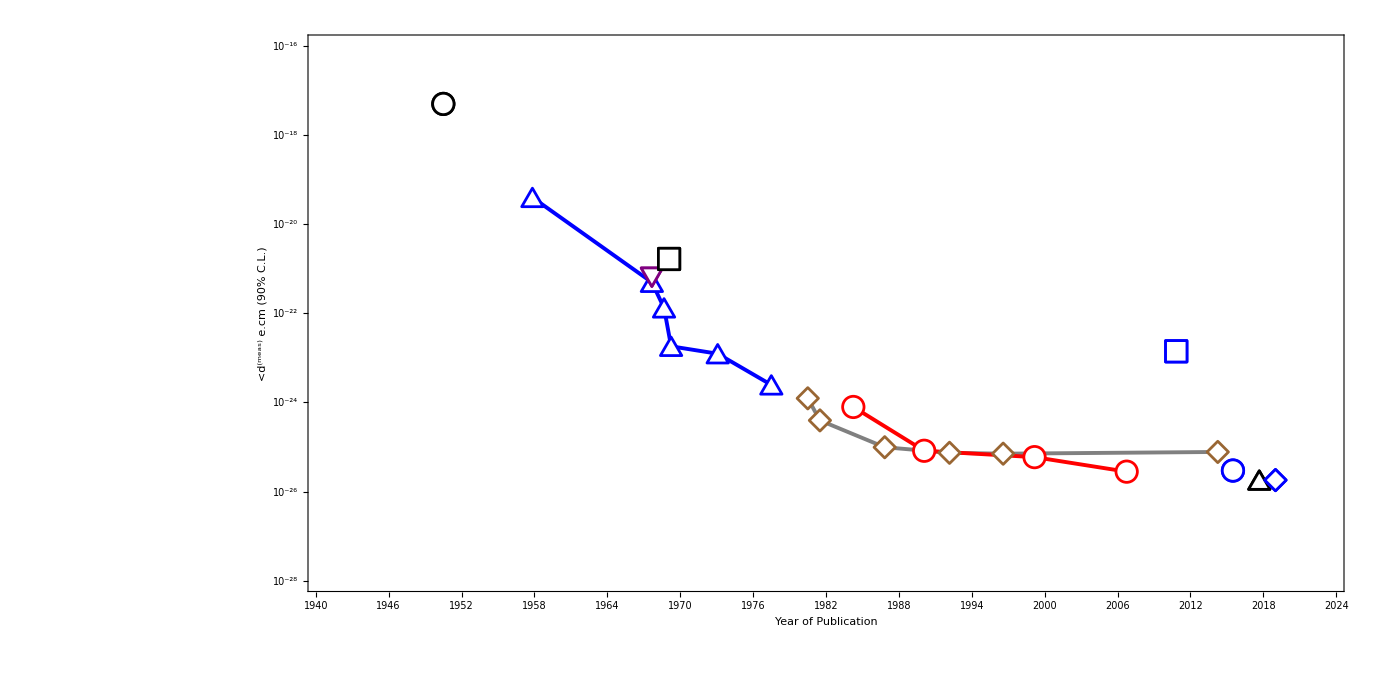

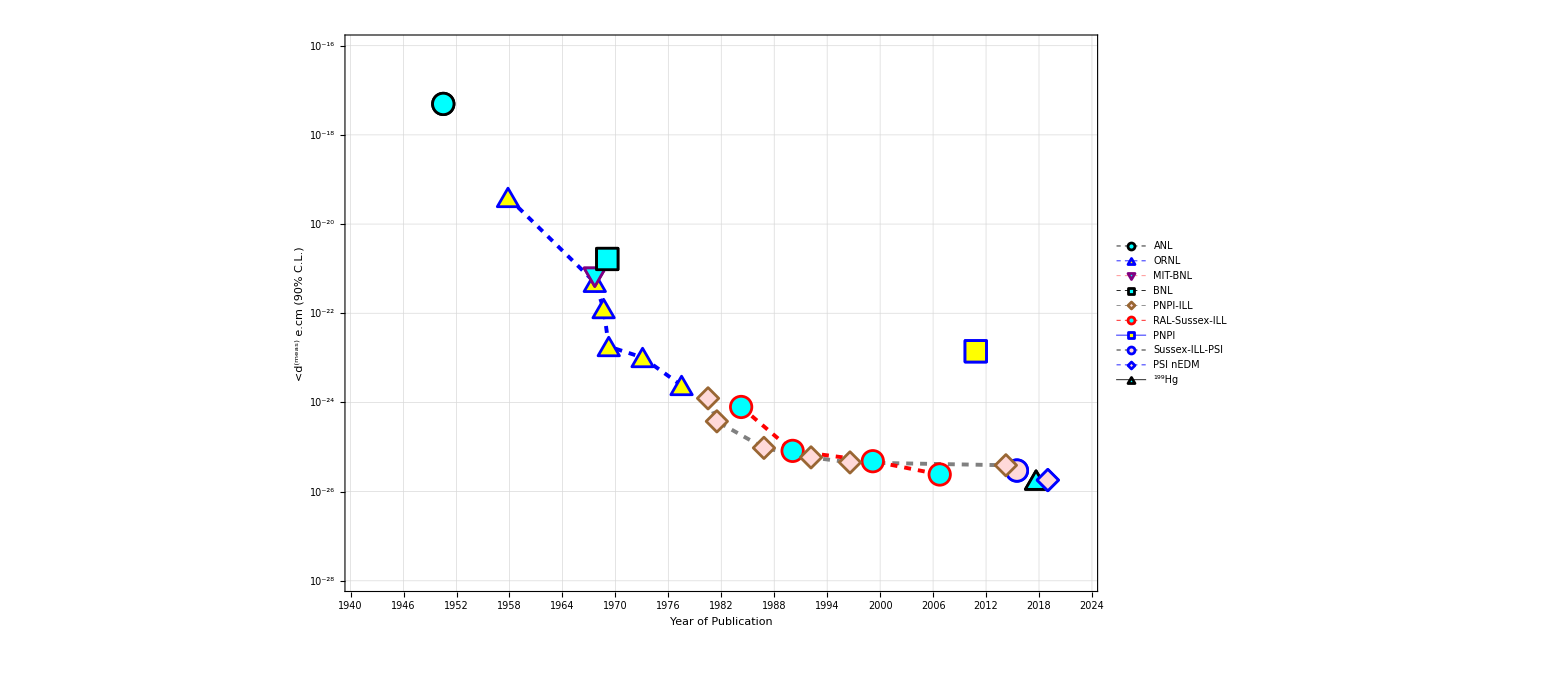

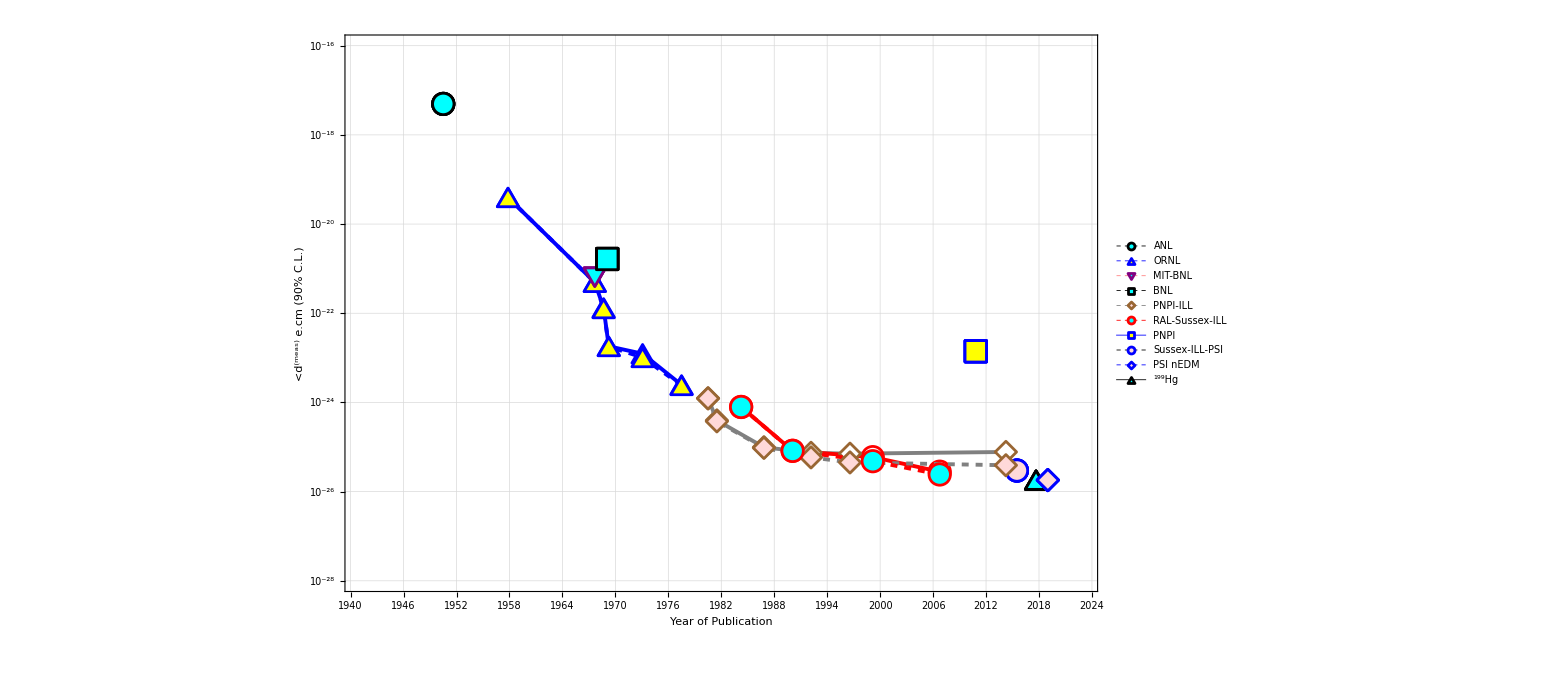

```mathematica
puredat=Table[Transpose[{acdat[[k]][[;;,1]],acdat[[k]][[;;,2]][[;;,2]]*1.6485}],{k,1,szdat}]
cumdat=Table[Table[{acdat[[k]][[;;,1]][[l]],1/Sqrt[Sum[(1/(1.64835^2*acdat[[k]][[;;,2]][[;;,2]][[m]]^2)),{m,1,l}]]},{l,1,Dimensions[acdat[[k]][[;;,2]][[;;,2]]][[1]]}],{k,1,szdat}]
cht2=Show[{
ListLogPlot[puredat,Frame->True,Joined->True,PlotRange->{{1941,2023},{N[10^(ptsty+2)],N[10^(pteny-1)]}},Frame->True,FrameStyle->Thickness[thk],FrameTicksStyle->{Directive[Black,Thickness[thk]],Directive[Black,Thickness[thk]]},FrameLabel->{"Year of Publication","<d^(meas) e.cm (90% C.L.)"},LabelStyle->{28,Black,Bold},TicksStyle->{Directive[FontSize->28]},GridLines->Automatic,Joined->True,
FrameTicks->{(*y,x*){tk2[ptsty,pteny,.02,0,0,0,ptinty],tk2[ptsty,pteny,.02,0,0,0,ptinty]},{tk3[1940,2030,.02,0,0,0,6],None}},AspectRatio->.5,ImageSize->1400,
PlotStyle->{{Black,Thickness[thk/1.5]},{Blue,Thickness[thk/1.5]},{Pink,Thickness[thk/1.5]},{Black,Thickness[thk/1.5]},{Gray,Thickness[thk/1.5]},{Red,Thickness[thk/1.5]},{Blue,Thickness[thk/1.5]},{Black,Thickness[thk/1.5]},{Blue,Thickness[thk/1.5]},{Black,Thickness[thk/1.5]}},PlotMarkers->{circle[White,Black],triangle[White,Blue],triangle2[White,Purple],square[White,Black],diamond[White,Brown],circle[White,Red],square[White,Blue],circle[White,Blue],diamond[White,Blue],triangle[White,Black]}]
}]
cht3=Show[{
ListLogPlot[cumdat,Frame->True,Joined->True,PlotRange->{{1941,2023},{N[10^(ptsty+2)],N[10^(pteny-1)]}},Frame->True,FrameStyle->Thickness[thk],FrameTicksStyle->{Directive[Black,Thickness[thk]],Directive[Black,Thickness[thk]]},FrameLabel->{"Year of Publication","<d^(meas) e.cm (90% C.L.)"},LabelStyle->{28,Black,Bold},TicksStyle->{Directive[FontSize->28]},GridLines->Automatic,Joined->True,
FrameTicks->{(*y,x*){tk2[ptsty,pteny,.02,0,0,0,ptinty],tk2[ptsty,pteny,.02,0,0,0,ptinty]},{tk3[1940,2030,.02,0,0,0,6],None}},AspectRatio->.5,ImageSize->1400,
PlotStyle->{{Black,Thickness[thk/1.5],Dashed},{Blue,Thickness[thk/1.5],Dashed},{Pink,Thickness[thk/1.5],Dashed},{Black,Thickness[thk/1.5],Dashed},{Gray,Thickness[thk/1.5],Dashed},{Red,Thickness[thk/1.5],Dashed},{Blue,Thickness[thk/1.5]},{Black,Thickness[thk/1.5],Dashed},{Blue,Thickness[thk/1.5],Dashed},{Black,Thickness[thk/1.5]}},PlotMarkers->{circle[Cyan,Black],triangle[Yellow,Blue],triangle2[Cyan,Purple],square[Cyan,Black],diamond[LightRed,Brown],circle[Cyan,Red],square[Yellow,Blue],circle[LightRed,Blue],diamond[LightRed,Blue],triangle[Cyan,Black]},PlotLegends->LineLegend[Style[#,22]&/@{"ANL","ORNL","MIT-BNL","BNL","PNPI-ILL","RAL-Sussex-ILL","PNPI","Sussex-ILL-PSI","PSI nEDM","^199Hg"},LegendMarkerSize->{24,24}]]
}]
cht4=Show[{cht2,cht3}]
```

```mathematica
Export[StringJoin[PicDir,seperator,"EDM_time_data.png"],cht]
Export[StringJoin[PicDir,seperator,"EDM_time_limits_pure.png"],cht2]
Export[StringJoin[PicDir,seperator,"EDM_time_limits_cumu.png"],cht3]
Export[StringJoin[PicDir,seperator,"EDM_time_limits.png"],cht4]
```

C:\Users\tmpra\Dropbox\nEDM\Pictures\EDM_time_data.png

C:\Users\tmpra\Dropbox\nEDM\Pictures\EDM_time_limits_pure.png

C:\Users\tmpra\Dropbox\nEDM\Pictures\EDM_time_limits_cumu.png

C:\Users\tmpra\Dropbox\nEDM\Pictures\EDM_time_limits.png